```mathematica
R[t_]:={{1,0,0},{0,Cos[t],Sin[t]},{0,-Sin[t],Cos[t]}};
f[x_]:=Sqrt[1-x^2];
a=-1;
b=1;
F[x_]:={x,f[x],0};
A[t_,x_]:=R[t].F[x];
```

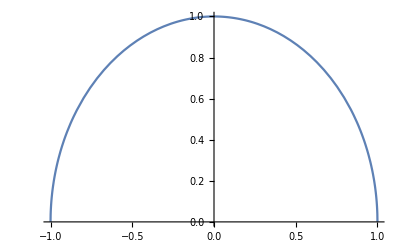

```mathematica
Plot[f[x],{x,a,b}]
```

```mathematica
Px=ParametricPlot3D[{x,0,0},{x,-1,1},PlotStyle->{Thick,Blue}];
Py=ParametricPlot3D[{0,x,0},{x,-1,1},PlotStyle->{Thick,Red}];
Pz=ParametricPlot3D[{0,0,x},{x,-1,1},PlotStyle->{Thick,Green}];
Pr[t_]:=ParametricPlot3D[A[t,x],{x,-1,1},PlotStyle->{Thick}];
```

```mathematica
Manipulate[Show[Px,Py,Pz,Pr[t],Boxed->False,Axes->False],{t,0,2*Pi}]
```

```mathematica
RevolutionPlot3D[f[x],{x,a,b},{t,0,2Pi},RevolutionAxis->{1, 0, 0}, Boxed->False]
```

-Graphics3D-

```mathematica
Ry[t_]:={{Cos[t],0,Sin[t]}, {0,1,0},{-Sin[t],0,Cos[t]}};
g[x_]:=Sqrt[x];
a=0;
b=1;
G[x_]:={x,g[x],0};
L1[y_]:={1/2,y,0};
L2[y_]:={1/2+0.1,y,0};
B[t_,x_]:=Ry[t].G[x];
BL1[t_,y_]:=Ry[t].L1[y];
BL2[t_,y_]:=Ry[t].L2[y];
```

```mathematica
P2x=ParametricPlot3D[{x,0,0},{x,-1,b},PlotStyle->{Thick,Blue}];
P2y=ParametricPlot3D[{0,x,0},{x,-1,b},PlotStyle->{Thick,Red}];
P2z=ParametricPlot3D[{0,0,x},{x,-1,b},PlotStyle->{Thick,Green}];
Pyr[t_]:=ParametricPlot3D[B[t,x],{x,a,b},PlotStyle->{Thick}];
L1yr[t_]:=ParametricPlot3D[BL1[t,y],{y,0,Sqrt[1/2]},PlotStyle->{Thick}];
L2yr[t_]:=ParametricPlot3D[BL2[t,y],{y,0,Sqrt[1/2+0.1]},PlotStyle->{Thick}];
```

```mathematica
Manipulate[Show[P2x,P2y,P2z,Pyr[t],L1yr[t],L2yr[t],Boxed->False,Axes->False,AxesLabel->{X,Y,Z}],{t,0,2*Pi}]
```

```mathematica
RevolutionPlot3D[{x,g[x],0},{x,a,b},{t,0,2Pi},RevolutionAxis->{0, 1, 0}, Boxed->False, AxesLabel->{X,Y,Z}, ViewPoint->{-2,-2,0}]
```

-Graphics3D-